```mathematica
ClearAll["Global`*"]
```

```mathematica
myplotStyle={PlotStyle->Directive[Thick],LabelStyle->Directive[FontSize->12],GridLinesStyle->Directive[Gray,Dashed],ImageSize->{500},PlotRangePadding->0.1,PlotRangeClipping->False,AxesOrigin->{0,0},Frame->True,FrameTicks->{{Automatic,Automatic},{None,None}}};
```

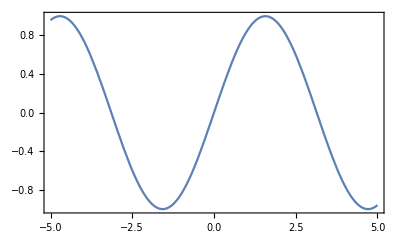

```mathematica
p=Plot[Sin[x],{x,-5,5},PlotRangeClipping->False,Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImagePadding->{{20, 20}, {25, 20}},FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Directive[FontOpacity->0,FontSize->0],Directive[FontOpacity->0,FontSize->0]}}];
Show[{p,Graphics[{Text[Style[#,12],{#,-1.19}]&/@Table[i,{i,-5,5,1}]}],Graphics[{Text[Style["x",12],{0,-1.3}]}]}]
```